```mathematica
Clear[By,Bz,By0,Bz0,R,d]
```

```mathematica
(*两个平行线圈的磁场*)
```

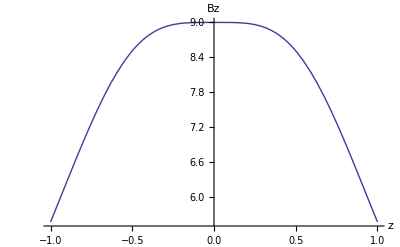

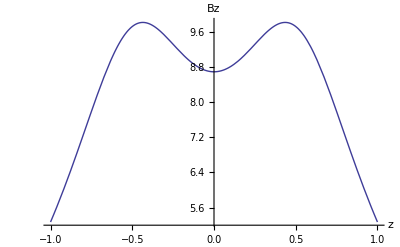

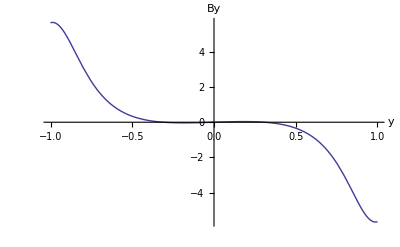

```mathematica
By0[y_,z_]:=NIntegrate[(R z Sin[φ])/((R^2+y^2+z^2-2 R y Sin[φ])^(3/2)),{φ,0,2π}];
Bz0[y_,z_]:=NIntegrate[(R(R-y Sin[φ]))/((R^2+y^2+z^2-2 R y Sin[φ])^(3/2)),{φ,0,2π}];
R=1.0;d=R;
By[y_,z_]:=By0[y,z-d/2]+By0[y,z+d/2];
Bz[y_,z_]:=Bz0[y,z-d/2]+Bz0[y,z+d/2];
Plot[Bz[0,z],{z,-d,d},AxesLabel->{"z","Bz"},PlotRange->All]
Plot[Bz[R/2,z],{z,-d,d},AxesLabel->{"z","Bz"},PlotRange->All]
Plot[By[y,d/4],{y,-R,R},AxesLabel->{"y","By"},PlotRange->All]
```

```mathematica
(*磁力线，折线法*)
```

```mathematica
By0[y_,z_]:=NIntegrate[(R z Sin[φ])/((R^2+y^2+z^2-2 R y Sin[φ])^(3/2)),{φ,0,2π}];
Bz0[y_,z_]:=NIntegrate[(R(R-y Sin[φ]))/((R^2+y^2+z^2-2 R y Sin[φ])^(3/2)),{φ,0,2π}];
R=1.0;d=R;
By[y_,z_]:=By0[y,z-d/2]+By0[y,z+d/2];
Bz[y_,z_]:=Bz0[y,z-d/2]+Bz0[y,z+d/2];
r1=step=0.005R;r2=2R;
forceline={};p1={-R,d/2};p2={R,d/2};p3={-R,-d/2};p4={R,-d/2};
Do[p={r1,z0};single={};While[(Abs[p[[1]]]≥r1)∧(Norm[p]<r2),AppendTo[single,p];θ=Arg[By[p[[1]],p[[2]]]+ⅈ*Bz[p[[1]],p[[2]]]];p=p-step*{Cos[θ],Sin[θ]}];
AppendTo[forceline,single];m=Length[single];single=Table[{-single[[j,1]],single[[j,2]]},{j,m}];AppendTo[forceline,single],{z0,-0.9d/2.0,0.9d/2.0,0.1d/2.0}]
Show[Graphics[{Line/@forceline}],Axes->True,AxesLabel->{"y","z"},AspectRatio->1,Epilog->{PointSize[0.02],Point/@{p1,p2,p3,p4}}]
```

```mathematica
Clear[By,Bz,By0,Bz0,R,d,r1,step,r2,forceline,p1,p2,p3,p4,p,single,θ,m]
```